# Cuaderno de Prácticas

## Análisis y métodos numéricos

## Grado en Ingeniería Informática

## CURSO 2024/25

## Datos personales

Nombre y apellidos : Francisco Javier Martín - Lunas Escobar
DNI : 26268082
Grupo de teoría : 2
Grupo de prácticas :

## Práctica 6

Derivadas

```mathematica
f[x_]:=Sin[x]/Cos[x];
f'[x]
```

Sec[x]^2

```mathematica
f''[x]
```

2 Sec[x]^2 Tan[x]

### Derivada séptima de x

```mathematica
D[f[x],{x,7}]
```

272 Sec[x]^8+2880 Sec[x]^6 Tan[x]^2+1824 Sec[x]^4 Tan[x]^4+64 Sec[x]^2 Tan[x]^6

Derivada de f[x] 5 veces y después calcular f’’’’’[0]

```mathematica
D[f[x],{x,5}]/.x->0
```

16

### Comprobar derivadas hechas a mano

```mathematica
f'[x]
```

Sec[x]^2

Está bien

```mathematica
Sec[x]^2==(Cos[x]Cos[x]+Sin[x]Sin[x])/Cos[x]^2//Simplify
```

True

```mathematica
Simplify[%]
```

Sec[x]^2

### Derivación implícita

Para la derivación implícitas, escribimos la expresión especificando en este caso que y depende de x

```mathematica
D[x^2+y[x]^2==1,x]
```

2 x+2 y[x] y'[x]==0

### Recta tangente

La RT es la recta que pasa por un punto de la función y tiene su misma pendiente

```mathematica
f[x_]:=E^x Cos[x]
```

```mathematica
f[0]+f'[0](x-0)
```

1+x

```mathematica
r[x_]:=1+x
```

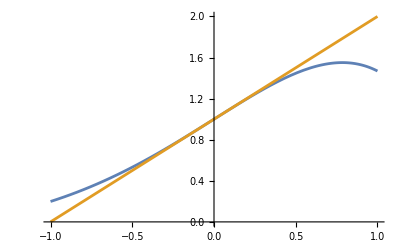

```mathematica
Plot[{f[x],r[x]},{x,-1,1}]
```

Estudio del signo, crecimiento y convexidad de una función

```mathematica
f[x_]:=x^3-4x+8
```

Se estudia: el dominio de f, la continuidad de f, los ceros de f y se forman intervalos para evaluar f en ellos.
Como es un polinomio, el dominio es toda una recta real y siempre es continua. Falta estudiar los ceros de f.

```mathematica
Solve[f[x]==0,x]//N
```

{{}}

Solo hay un cero real, -2, 649...

Evaluamos f en un punto anterior y otro posterior

```mathematica
{f[-3],f[0]}
```

{-7,8}

f es negativa hasta el - 2.649 ... y positiva después .
  Para el crecimiento hacemos lo mismo, pero para la función f’[x]

```mathematica
Solve[f'[x]==0,x]//N
```

{{x→-1.1547},{x→1.1547}}

Se anula en dos puntos. Hay que evaluar en un punto anterior, en otro entre los dos puntos y en uno mayor.

```mathematica
{f'[-2],f'[0],f[2]}
```

{8,-4,8}

f' es positiva antes de - 1.15, negativa entre - 1.15 y 1.15 y es positiva después de 1.15. 
Por tanto, f es creciente hasta -1.15, decreciente entre -1.15 y 1.15 y creciente después de 1.15. Tiene un máximo local en -1.15 y un mínimo local en 1.15.

Para estudiar la convexidad, estudiamos los signos f’[x].

```mathematica
f''[x]
```

6 x

```mathematica
Solve[f''[x]==0,x]
```

{{x→0}}

```mathematica
{f''[-1],f''[1]}
```

{-6,6}

f'' es negativa desde - infinito hasta el 0, y es positiva desde 0 a + infinito . f' es decreciente desde - infinito hasta el 0 y creciente de 0 a + infinito.
f es (∩) desde - infinito a 0 y f es ∪ de 0 a infinito. f tiene 0 en un punto de inflexión

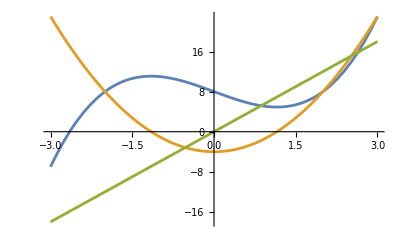

```mathematica
Plot[{f[x], f'[x],f''[x]}, {x,-3,3}]
```